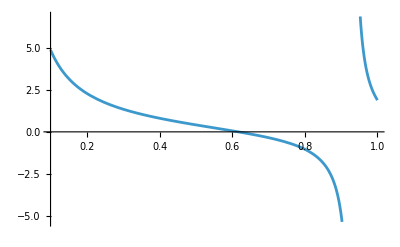

```mathematica
ClearAll["Global`*"]; 
u[x_]:=Cot[Sinh[2x]]; 
Plot[u[x],{x,0.1,1}]

error[h_]:=Block[{},{
xi=0.25;c=0.01;
uvalueFD={u[xi-h],u[xi],u[xi+h]};
uvalueRFD5={u[xi-2h],u[xi-h],u[xi],u[xi+h],u[xi+2h]};
uvaluePM={u[xi-2h],u[xi-h],u[xi],u[xi+h],u[xi+2h]};
uvalueHFD={u'[xi-h],u[xi-h],u[xi],u[xi+h],u'[xi+h]};
derivative=u'[xi];
(*FD3*)
setweights1={-1/(2 h),0,1/(2 h)};
functionval1=setweights1.uvalueFD;
(*RBF-FD3*)
setweights2={-1/(2 h)-(3h)/(4 c^2),0,-(-1/(2 h)-(3h)/(4 c^2))};
functionval2=setweights2.uvalueFD;
(*RBF-FD5*)
setweights3={((-355 h^4)/c^4+(100 h^2)/c^2+8)/(96h),-(625 h^3)/(48 c^4)-(25h)/(12 c^2)-2/(3 h),0,-(-(625 h^3)/(48 c^4)-(25h)/(12 c^2)-2/(3 h)),-(((-355 h^4)/c^4+(100 h^2)/c^2+8)/(96h))};
functionval3=setweights3.uvalueRFD5;
(*RBF-HFD*)
setweights4={-1/4-(3 h^2)/(16 c^2),-3/(4 h)-(3h)/(16 c^2),0,-(-3/(4 h)-(3h)/(16 c^2)),-1/4-(3 h^2)/(16 c^2)};
functionval4=setweights4.uvalueHFD;

(*RBF-HFDnew*)
setweightsnew={-1/4-(3 h^2)/(20 c^2),-3/(4 h)-(3 h)/(20 c^2),0,3/(4 h)+(3 h)/(20 c^2),-1/4-(3 h^2)/(20 c^2)};
functionval5=setweightsnew.uvalueHFD;

Flatten@Abs@{derivative-functionval1,derivative-functionval2,derivative-functionval3,derivative-functionval4,derivative-functionval5}
}][[1]]
```

7.05148-2.00502 x

17.0966-2.00448 x

35.1907-4.00957 x

19.9684-4.01005 x

19.6472-4.01005 x

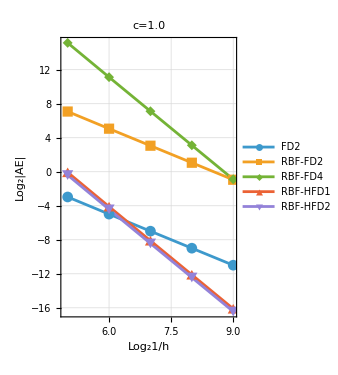

```mathematica
min=5;max=9;
error11=Log[2,N[Table[{1/j,error[j][[1]]},{j,Table[1/2^h,{h,min,max}]}]]];
fit1=Fit[error11,{1,x},x]
error12=Log[2,N[Table[{1/j,error[j][[2]]},{j,Table[1/2^h,{h,min,max}]}]]];
fit2=Fit[error12,{1,x},x]
error13=Log[2,N[Table[{1/j,error[j][[3]]},{j,Table[1/2^h,{h,min,max}]}]]];
fit3=Fit[error13,{1,x},x]
error14=Log[2,N[Table[{1/j,error[j][[4]]},{j,Table[1/2^h,{h,min,max}]}]]];
fit4=Fit[error14,{1,x},x]
error15=Log[2,N[Table[{1/j,error[j][[5]]},{j,Table[1/2^h,{h,min,max}]}]]];
fit5=Fit[error15,{1,x},x]

ListPlot[{error11,error12,error13,error14,error15},PlotRange->All,Joined->True,
PlotMarkers->Automatic,FrameLabel->{"Log_21/h","Log_2|AE|"},
PlotLabel->"c=1.0",
AspectRatio->1.5,(*PlotStyle->{Purple,Gray,Blue,Red},*)
PlotMarkers->{Automatic,Offset[2]},
PlotLegends->Placed[
{Style["FD2",9],
Style["RBF-FD2",9],
Style["RBF-FD4",9],
Style["RBF-HFD1",9],
Style["RBF-HFD2",9]
},
{Left,Bottom}],
PlotTheme->"Detailed",ImageSize->250
]
```

```mathematica
resul1=Transpose@{Flatten@Table[{j},{j,Table[1/2^h,{h,min,max}]}],
Flatten@Table[ScientificForm[error[j][[1]]],{j,Table[1/2^h,{h,min,max}]}],
Flatten@Table[ScientificForm[error[j][[2]]],{j,Table[1/2^h,{h,min,max}]}],
Flatten@Table[ScientificForm[error[j][[3]]],{j,Table[1/2^h,{h,min,max}]}],
Flatten@Table[ScientificForm[error[j][[4]]],{j,Table[1/2^h,{h,min,max}]}],
Flatten@Table[ScientificForm[error[j][[5]]],{j,Table[1/2^h,{h,min,max}]}]
};
TableForm[resul1]
TeXForm[resul1]
```

1/32 | 1.27882×10^-1 | 1.35299×10^2 | 3.64946×10^4 | 9.53425×10^-1 | 7.63143×10^-1
1/64 | 3.15966×10^-2 | 3.34718×10^1 | 2.22996×10^3 | 5.82037×10^-2 | 4.65876×10^-2
1/128 | 7.87613×10^-3 | 8.34621 | 1.38613×10^2 | 3.61656×10^-3 | 2.89478×10^-3
1/256 | 1.9676×10^-3 | 2.0852 | 8.65156 | 2.25706×10^-4 | 1.8066×10^-4
1/512 | 4.9181×10^-4 | 5.21215×10^-1 | 5.4054×10^-1 | 1.41015×10^-5 | 1.12872×10^-5

\left(
\begin{array}{cccccc}
 \frac{1}{32} & 1.27882\times 10^{-1} & 1.35299\times 10^2 & 3.64946\times 10^4 & 9.53425\times 10^{-1} & 7.63143\times 10^{-1} \\
 \frac{1}{64} & 3.15966\times 10^{-2} & 3.34718\times 10^1 & 2.22996\times 10^3 & 5.82037\times 10^{-2} & 4.65876\times 10^{-2} \\
 \frac{1}{128} & 7.87613\times 10^{-3} & 8.34621 & 1.38613\times 10^2 & 3.61656\times 10^{-3} & 2.89478\times 10^{-3} \\
 \frac{1}{256} & 1.9676\times 10^{-3} & 2.0852 & 8.65156 & 2.25706\times 10^{-4} & 1.8066\times 10^{-4} \\
 \frac{1}{512} & 4.9181\times 10^{-4} & 5.21215\times 10^{-1} & 5.4054\times 10^{-1} & 1.41015\times 10^{-5} & 1.12872\times 10^{-5} \\
\end{array}
\right)